```mathematica
σ = 0.5;
h = 0.01;
τ = 0.005;
```

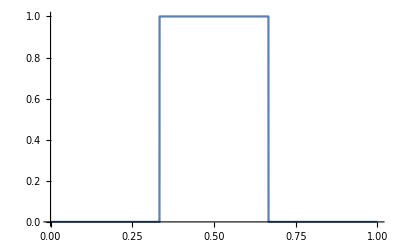

```mathematica
(* выберем в U0 начальные условия *)
ClearAll[U0];
U0[x_] := UnitStep[x-1/3]-UnitStep[x-2/3];
Plot[U0[x], {x, 0, 1}]
```

```mathematica
(* отобразить точки *)
GetPlot[Udots_] := Module[{data},
data = Transpose[{grid, Udots}];
Show[{
ListLinePlot[data, PlotRange->{{0, 1}, {-0.5, 1.5}}],
Plot[U0[x], {x,0, 1}, PlotStyle->{Red, Dashed, Opacity[0.5]}]
}]
]
```

```mathematica
(* сделаем сетку с шагом h *)
grid = Range[0, 1,h];
U0dots = Map[U0, grid];
Ν = Length@U0dots;
```

## Коэффициенты C, B3, B5

```mathematica
(* сохраним все коэффициенты С*)
ClearAll[coefC];
coefC[-2] = 1/6 σ (σ^2-1);
coefC[-1] = 1/2 σ (-σ^2 + σ  +2);
coefC[0] = 1/2(σ^3-2 σ^2 - σ + 2);
coefC[1] = - 1/6 σ (σ^2 - 3 σ + 2);
```

```mathematica
(* сохраним все коэффициенты B3*)
ClearAll[coefB3];
coefB3[-2]=0;
coefB3[-1]=1/2 σ (σ+1);
coefB3[0]=1-σ^2;
coefB3[1]=1/2 σ (σ-1);
```

```mathematica
(* сохраним все коэффициенты B5*)
ClearAll[coefB5];
coefB5[-2]=1/2 σ (σ-1);
coefB5[-1]=σ (2-σ);
coefB5[0]=1/2(σ^2-3 σ + 2);
coefB5[1]=0;
```

```mathematica
(* создадим разреженную матрицу эволюции *)
GetEvolMat[coef_] := Module[{EvolMat, Rules, TmpRules, i},
Rules = {};
For[i=3, i <=Ν-2, i++,
TmpRules = {
{i, i-2} -> coef[-2],
{i, i-1} -> coef[-1],
{i, i} ->   coef[0],
{i, i+1} ->  coef[1]
};
Rules = Join[Rules, TmpRules];
];
Rules = Join[Rules, {
{1, 1} -> coef[0], {1, 2} -> coef[1], {1, Ν-1} -> coef[-2], {1, Ν} -> coef[-1],
{2, 1} -> coef[-1], {2, 2} -> coef[0], {2,3} -> coef[1], {2, Ν} -> coef[-2],
{Ν-1, Ν-3} -> coef[-2], {Ν-1, Ν-2} -> coef[-1], {Ν-1,Ν-1} -> coef[0], {Ν-1, Ν} -> coef[1],
{Ν, 1} -> coef[1], {Ν, Ν-2} -> coef[-2], {Ν, Ν-1} -> coef[-1], {Ν,Ν} -> coef[0]
}];
EvolMat = SparseArray[Rules, {Ν, Ν}];
EvolMat]
```

```mathematica
EvolMatC = GetEvolMat[coefC];
EvolMatB3 = GetEvolMat[coefB3];
EvolMatB5 = GetEvolMat[coefB5];
```

```mathematica
(* возьмём 3 отображений *)
EvolMat = 1/3(EvolMatC+EvolMatB5+EvolMatB3);
```

## Эволюция

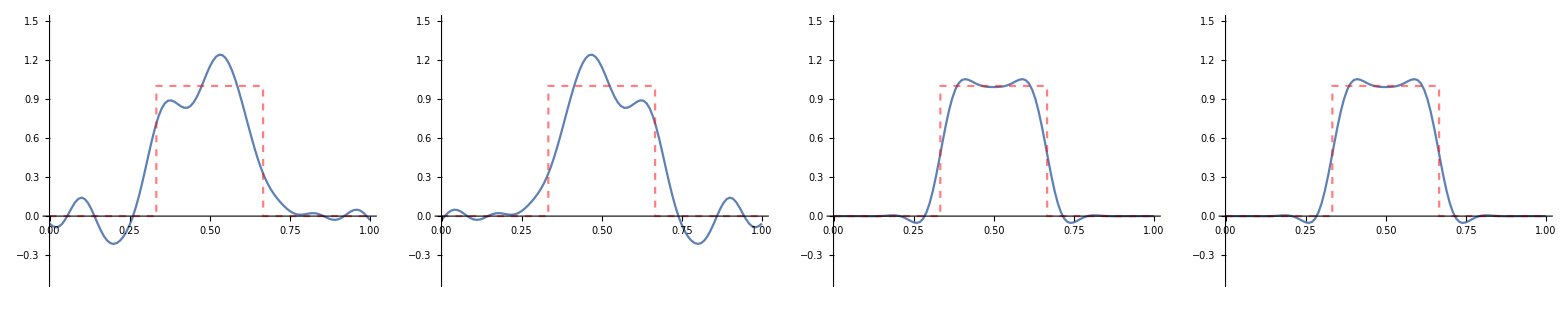

```mathematica
(* посмотрим на размытие через 1000 шагов для B3, B5, C, суперпозиции *)
n = 1010;
resC = Nest[EvolMatC.#&, U0dots, n];
resB3 = Nest[EvolMatB3.#&, U0dots, n];
resB5 = Nest[EvolMatB5.#&, U0dots, n];
res = Nest[EvolMat.#&, U0dots, n];
Multicolumn[Map[GetPlot, {resB3, resB5, resC, res}], {1, 4}]
```